```mathematica
ClearAll["Global'*"]
```

```mathematica
CPair[x_,y_]:=0.5(x+y)(x+y+1)+y
K:=CPair[128,128]/Log[CPair[128,128]]
Assuming[A>0,Reduce[A==x/Log[x]-K,x]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

4.34649×10^9+1.36946×10^6 A≠0&&-1.+x≠0&&((Im[ProductLog[-1,-1369464/(4346489501+1369464 A)]]≥-3.14159&&x==2.71828^(-1. ProductLog[-1,-1369464/(4346489501+1369464 A)]))||x==2.71828^(-1. ProductLog[-1369464/(4346489501+1369464 A)])||(Im[ProductLog[1,-1369464/(4346489501+1369464 A)]]<3.14159&&x==2.71828^(-1. ProductLog[1,-1369464/(4346489501+1369464 A)])))

```mathematica
CPair[128,128]
```

33024.

```mathematica
2.718281828459045^(-1. ProductLog[1,-1369464/(4346489501+1369464 *10)])
```

33754.1-21832.8 ⅈ

```mathematica
-ProductLog[1,-1369464/(4346489501+1369464*10)]//N
```

10.6016-6.85732 ⅈ

```mathematica
Table[{2^i,PaddedForm[Reduce[2^i==x/Log[x]-K,x],5]},{i,3,11}]//TableForm
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

8 | x== 1.0003||x== 33116.
16 | x== 1.0003||x== 33208.
32 | x== 1.0003||x== 33393.
64 | x== 1.0003||x== 33761.
128 | x== 1.0003||x== 34500.
256 | x== 1.0003||x== 35982.
512 | x== 1.0003||x== 38961.
1024 | x== 1.0002||x== 44975.
2048 | x== 1.0002||x== 57202.

```mathematica
ClearAll["Global'*"]
```

```mathematica
lst:={{8,730},{16,184},{32,369},{64,737},{128,1476},{256,2958},{512,5937},{1024,11951},{2048,24178}}
lm:=Fit[lst,{1,x},x]//Normal
```

```mathematica
lm
```

68.9825+11.717 x

```mathematica
a:=ListPlot[lst,PlotStyle->{RGBColor[1,0,0],PointSize[Medium]}]
b:=Plot[68.9824902723752+11.71701506544732 x,{x,8,2048},PlotStyle->{RGBColor[0,0,1]}]
```

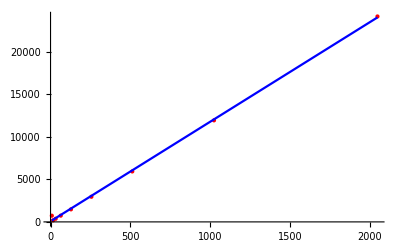
-Graphics-Block SizeMax(x)-C(128,128)

```mathematica
img=Labeled[Show[a,b,LabelStyle->Directive[Blue, Bold]],{"Block Size","Max(x)-C(128,128)"},{Left,Bottom},RotateLabel->True]
```